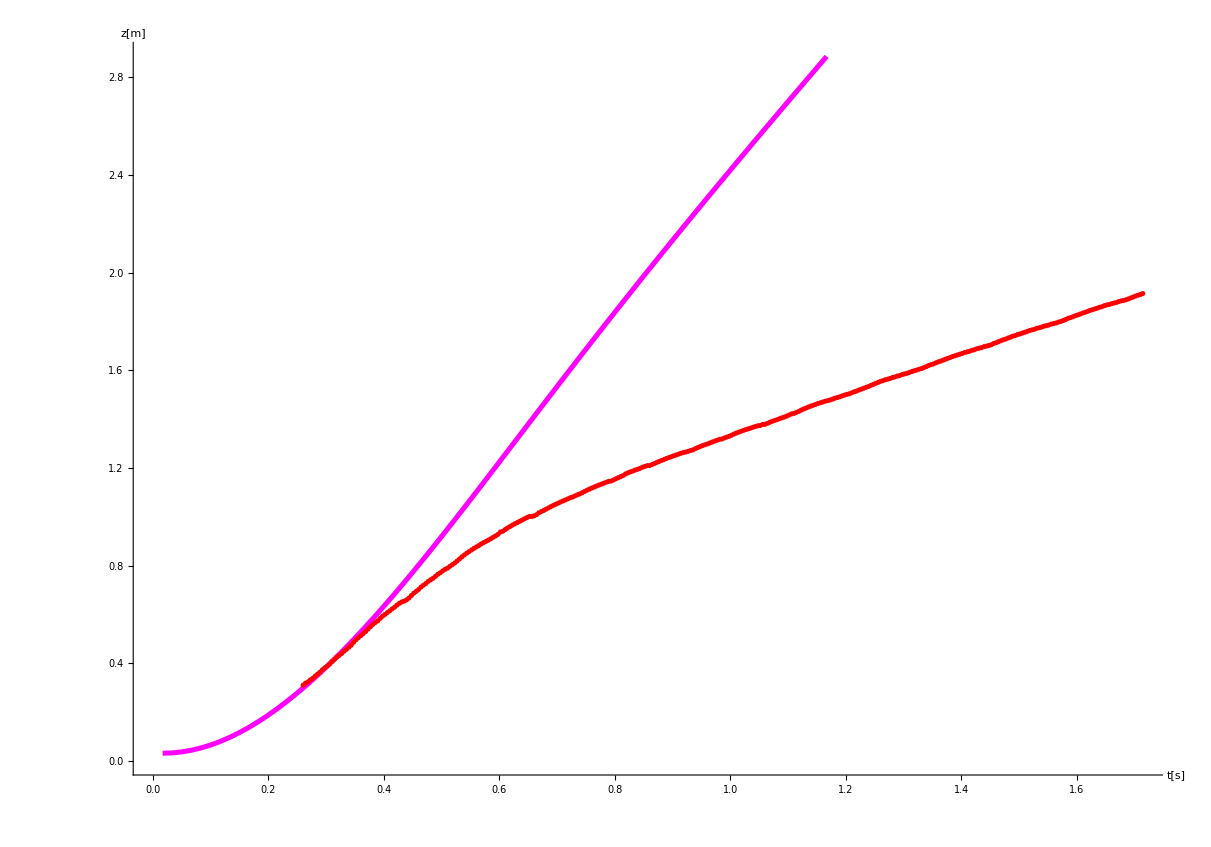

```mathematica
Clear["Global`*"];
ΔY0=.391;
ΔY=1.25;
ΔX0=.57;
resx=848;
fps=240;
Številke[kopirano_]:={
sezx=ΔY/ΔY0(-ΔX0/2+# ΔX0/resx)&/@(ToExpression[StringReplace[StringReplace[#,","->"."],"e"->"*10^"]]&/@Drop[StringSplit[kopirano,"
"],2]);
Table[{N[i/240],sezx[[i]]},{i,Length[sezx]}]
}[[1]];
podatki=Številke[Import["c:\\Users\\gal\\Downloads\\rn.aviončki\\103GOPRO\\obdelani\\H2.txt"]];
{t,v t+x0}/.FindFit[podatki,v t+x0,{v,x0},t];
podatki=(#-podatki[[1]]+{.26,.31})&/@podatki;



sezWp={-0.00027898207033130284,-0.00029123499044235457,-0.0003275628811063963,-0.0003877647168945013,-0.0004715144356704761,-0.0005783677464181803,-0.0007077738286238706,-0.000859095030015389,-0.0010316264791416312,-0.0012246083864258473,-0.0014372368728072546,-0.0016686815237412598,-0.0019181046513267166,-0.0021846712718673923,-0.002467550973596861,-0.0027659226627035393,-0.003078984297737461,-0.00340595796382885,-0.003746085980314452,-0.004098626249164264,-0.004462853290339857,-0.0048380595177460566,-0.005223550180290713,-0.005618635774855579,-0.006022628634917651,-0.006434841877026359,-0.006854585773445836,-0.0072811643043137544,-0.007713877113738942,-0.008152024193075955,-0.008594907947874323,-0.00904183493607921,-0.009492122311002325,-0.009945107049189257,-0.010400153717494424,-0.01085666008663696,-0.011314061134050833,-0.011771831957573793,-0.01222949240591988,-0.012686615093954755,-0.013142830858780805,-0.013597826916834699,-0.014051343096049452,-0.014503169801530437,-0.01495314056977037,-0.0154011211860716,-0.01584700317732174,-0.01629070182054031,-0.01673217063895721,-0.01717141389350489,-0.017608466357472534,-0.01804336226307864,-0.01847612508414978,-0.018906800101308647,-0.019335469089570654,-0.0197622100076152,-0.02018707773079699,-0.0206101481475155,-0.021031526962872173,-0.02145128847238638,-0.021869483615238557,-0.022286205968054276,-0.02270155005520231,-0.023115561736006505,-0.023528312792231058,-0.023939893387820647,-0.024350346464249217,-0.024759733248960934,-0.025168129814427058,-0.025575565185827716,-0.02598210111966522,-0.02638780384112907,-0.02679268461622014,-0.027196801539181307,-0.02760020519811905,-0.028002907293195867,-0.028404962923988683,-0.02880638998115933,-0.029207216354056785,-0.029607489928298557,-0.03000720250099024,-0.030406399918700037,-0.030805105547885413,-0.031203319823389346,-0.031601083393052606,-0.03199839440765287,-0.0323952891966798,-0.03279177279243559,-0.03318785328534698,-0.033583575341913134,-0.03397892529072124,-0.03437393819397751,-0.034768626323808775,-0.035163012630766564,-0.035557116491392135,-0.03595094729715936,-0.0363445547603436,-0.03673793173897014,-0.037131118268419555,-0.03752413523032867,-0.037917002245384385,-0.03830973611318681,-0.03870235407451897,-0.03909488233763593,-0.039487299837056906,-0.03987963635336259,-0.04027187507332984,-0.04066400379287784,-0.04105600487004173,-0.04144786739491452,-0.04183955409705764,-0.04223103593168307,-0.042622302466348676,-0.04301330938244316,-0.04340405755100584,-0.04379452845456638,-0.04418472049360642,-0.04457465310528519,-0.04496436342571021,-0.04535384849267639,-0.045743172198262586,-0.04613240072573236,-0.046521551312465305,-0.04691064271348911,-0.047299747574895315,-0.04768887812803763,-0.04807800689608444,-0.048467089835296184,-0.04885612583839249,-0.049245087735901694,-0.04963388278579585,-0.050022270443477304,-0.05041049419678589,-0.05079818286863492,-0.051185523126405175,-0.05157191801355803,-0.05195792314089557,-0.052342466163822335,-0.05272653498593373,-0.05310823709579158,-0.0534880716830978,-0.05386661529526599,-0.054241207069695804,-0.05461475809923421,-0.054990823247549,-0.05536838334356762,-0.05575227568397009,-0.05613854166036572,-0.05652328505742535,-0.05691052627808574,-0.05730168629368588,-0.05769006033523259,-0.058083014254056396,-0.058478564352018425,-0.05887559042667868,-0.05927335609951183,-0.05967186312190678,-0.06006979897126746,-0.06047122424841752,-0.06087530352127415,-0.061281117900351546,-0.061689288850104544,-0.06209824424439846,-0.06251150042623282,-0.06292500987895111,-0.0633427545407181,-0.06376214138570627,-0.06418579235362426,-0.06460934907631824,-0.0650323918115637,-0.06545520675303178,-0.06587591078325918,-0.06629498987497805,-0.06671046327917145,-0.06712237980049819,-0.06753492588005264,-0.06794736349890354,-0.06835541232142504,-0.06876708110292251,-0.06917701850014436,-0.0695880014233276,-0.07000118119162113,-0.0704142183214038,-0.07083050281991446,-0.07124875453485989,-0.07166925522649915,-0.07209294813552693,-0.07251463612196825,-0.07293941997897926,-0.07336649029321775,-0.07379514201174395,-0.0742231828508442,-0.07465244280369045,-0.07508231374438618,-0.075510183142026,-0.07593886081489162,-0.07636614919611608,-0.0767950884878103,-0.0772233754864241,-0.07765108388240366,-0.07807971663180517,-0.07850531674854799,-0.07893262382768959,-0.07935883248238482,-0.07978664620799586,-0.0802137780018651,-0.08064093462540801,-0.08106941529672969,-0.08149383476571155,-0.08192035728355565,-0.08234547077972978,-0.08277167699153386,-0.08319985186238239,-0.08362403464011715,-0.08405088784663495,-0.0844750986571611,-0.08489937627174052,-0.08532422910073387,-0.08574817354105466,-0.08617454842403749,-0.08660001892887666,-0.08702518623518331,-0.08745017987889209,-0.08787512885525646,-0.08830047848324628,-0.08872534006386523,-0.08915080405638415,-0.08957434184415783,-0.08999914974160328,-0.09042383219462288,-0.09084743996924506,-0.09127156778046956,-0.09169572735382009,-0.09212118617397753,-0.0925479268001672,-0.09297332036918456,-0.09340044294117861,-0.09382567324976518,-0.09425284446234342,-0.09468073688097736,-0.09510716001955663,-0.095537207531809,-0.09596436727631617,-0.0963938520271705,-0.09682216980831808,-0.09724927666851779,-0.09767893300341113,-0.09810551618387865,-0.09853490468081742,-0.09896098803016432,-0.09938520770013559,-0.0998101232162023,-0.1002310826513472,-0.10065178909215362,-0.10106960290951726,-0.10148589435243659,-0.10190393571452275,-0.10231858992340323,-0.10273113312017704,-0.10314409265202294,-0.10355715890988233,-0.10397156430373423,-0.10438430716709247,-0.10479757968202719,-0.10521153802281882,-0.10562785874501936,-0.10604596040541883,-0.10646385518659623,-0.10688190509417456,-0.10730200282598996,-0.10772490946539212,-0.10814615721497425,-0.10856938166144871,-0.10899250760774892,-0.10941593427489202,-0.10984050479039054,-0.11026390349723592,-0.11068886803883105,-0.1111141947575164,-0.11153881908721623,-0.11196414634642039,-0.1123889452800212,-0.11281554274834342,-0.11324435342643835,-0.1136715721132234,-0.1141012633237115,-0.11453056599457488,-0.1149596420286303,-0.11539150588723289,-0.11582025263299703,-0.11624964171480397,-0.1166801733868262,-0.11710918473066309,-0.11754040278836525,-0.11797006304884908,-0.11840143120458431,-0.1188334744553627,-0.11926633930414543,-0.11970048707452902,-0.1201346609512774,-0.12056866809974522};
mase={0.00017739894926408102,0.00017739894926408102,0.0003807999999999999,0.0001679999999999999};
gg=9.81;
g1=Show[
Graphics[{
RGBColor[{1,ž,1}/.ž->0],
Thickness[.003],

Line[

sdksd=-Take[sezWp,{1,70}]/(Total[mase]gg);
Table[{N[i/60],sdksd[[i]]},{i,Length[sdksd]}]

]
}
],

(*******)
Graphics[{
RGBColor[{1,0,0,1}],
PointSize[.003],
Point[#]
}]&/@podatki,
(*******)

Graphics[{
RGBColor[{1,0,0,0}],

Point[{0,0}]
}],

AxesLabel->{"t[s]","z[m]"},
LabelStyle->{FontFamily->"Comic Sans MS",4,RGBColor[0.,0.,0.]},

AxesStyle->Directive[Black,Arrowheads[{0,0.02},Thin]  ] ,
Axes->True,
AspectRatio->.7


]
```

```mathematica
Export["c:\\Users\\gal\\Downloads\\rn.aviončki\\grafi\\z(t) helikopterja.pdf",%]
```

c:\Users\gal\Downloads\rn.aviončki\grafi\z(t) helikopterja.pdf

```mathematica
SystemOpen["c:\\Users\\gal\\Downloads\\rn.aviončki\\grafi\\z(t) helikopterja.pdf"]
```

```mathematica
SystemOpen["c:\\Users\\gal\\Downloads\\rn.aviončki\\grafi\\z(t) helikopterja.pdf"]
```

```mathematica
SystemOpen["c:\\Users\\gal\\Downloads\\rn.aviončki\\grafi\\z(t) helikopterja.pdf"]
```

```mathematica
SystemOpen["c:\\Users\\gal\\Downloads\\rn.aviončki\\grafi\\z(t) helikopterja.pdf"]
```

```mathematica
SystemOpen["c:\\Users\\gal\\Downloads\\rn.aviončki\\grafi\\z(t) helikopterja.pdf"]
```

```mathematica
SystemOpen["c:\\Users\\gal\\Downloads\\rn.aviončki\\grafi\\z(t) helikopterja.pdf"]
```

```mathematica
SystemOpen["c:\\Users\\gal\\Downloads\\rn.aviončki\\grafi\\z(t) helikopterja.pdf"]
```

```mathematica
SystemOpen["c:\\Users\\gal\\Downloads\\rn.aviončki\\grafi\\z(t) helikopterja.pdf"]
```

```mathematica
SystemOpen["c:\\Users\\gal\\Downloads\\rn.aviončki\\grafi\\z(t) helikopterja.pdf"]
```

```mathematica
velčrk
```

9

```mathematica
podatki
```

{{0.,0.},{0.00416667,0.00841645},{0.00833333,0.0137886},{0.0125,0.022026},{0.0166667,0.0284727},{0.0208333,0.0376054},{0.025,0.0453056},{0.0291667,0.0531848},{0.0333333,0.0632129},{0.0375,0.0712712},{0.0416667,0.0782551},{0.0458333,0.0868506},{0.05,0.0970578},{0.0541667,0.105832},{0.0583333,0.114965},{0.0625,0.122128},{0.0666667,0.129828},{0.0708333,0.13914},{0.075,0.14684},{0.0791667,0.155615},{0.0833333,0.164031},{0.0875,0.176208},{0.0916667,0.186415},{0.0958333,0.194832},{0.1,0.203248},{0.104167,0.211844},{0.108333,0.220081},{0.1125,0.230288},{0.116667,0.2396},{0.120833,0.249091},{0.125,0.25697},{0.129167,0.263417},{0.133333,0.273445},{0.1375,0.282578},{0.141667,0.28992},{0.145833,0.297441},{0.15,0.304783},{0.154167,0.312662},{0.158333,0.31943},{0.1625,0.328168},{0.166667,0.335387},{0.170833,0.341085},{0.175,0.344358},{0.179167,0.349633},{0.183333,0.357251},{0.1875,0.367459},{0.191667,0.376949},{0.195833,0.384471},{0.2,0.39235},{0.204167,0.401841},{0.208333,0.409541},{0.2125,0.416704},{0.216667,0.425299},{0.220833,0.432104},{0.225,0.437834},{0.229167,0.445893},{0.233333,0.454488},{0.2375,0.460577},{0.241667,0.468098},{0.245833,0.474544},{0.25,0.479379},{0.254167,0.486901},{0.258333,0.49379},{0.2625,0.500525},{0.266667,0.508568},{0.270833,0.516981},{0.275,0.525513},{0.279167,0.533488},{0.283333,0.540659},{0.2875,0.547503},{0.291667,0.554003},{0.295833,0.560254},{0.3,0.566355},{0.304167,0.571661},{0.308333,0.57865},{0.3125,0.584021},{0.316667,0.589034},{0.320833,0.594204},{0.325,0.599673},{0.329167,0.605902},{0.333333,0.611536},{0.3375,0.617991},{0.341667,0.627372},{0.345833,0.630875},{0.35,0.63767},{0.354167,0.64411},{0.358333,0.649944},{0.3625,0.655937},{0.366667,0.661165},{0.370833,0.666188},{0.375,0.671303},{0.379167,0.676307},{0.383333,0.681557},{0.3875,0.686486},{0.391667,0.690847},{0.395833,0.691223},{0.4,0.693909},{0.404167,0.698458},{0.408333,0.706183},{0.4125,0.711183},{0.416667,0.715777},{0.420833,0.720931},{0.425,0.726444},{0.429167,0.731495},{0.433333,0.736674},{0.4375,0.741036},{0.441667,0.745707},{0.445833,0.750271},{0.45,0.754603},{0.454167,0.758748},{0.458333,0.763022},{0.4625,0.76766},{0.466667,0.770784},{0.470833,0.775291},{0.475,0.779972},{0.479167,0.783576},{0.483333,0.788513},{0.4875,0.793581},{0.491667,0.798756},{0.495833,0.803208},{0.5,0.807615},{0.504167,0.811677},{0.508333,0.815923},{0.5125,0.819854},{0.516667,0.823693},{0.520833,0.82736},{0.525,0.831257},{0.529167,0.834967},{0.533333,0.836273},{0.5375,0.840638},{0.541667,0.845405},{0.545833,0.85024},{0.55,0.854295},{0.554167,0.858539},{0.558333,0.86537},{0.5625,0.869755},{0.566667,0.873828},{0.570833,0.876934},{0.575,0.881123},{0.579167,0.88448},{0.583333,0.888016},{0.5875,0.892527},{0.591667,0.895968},{0.595833,0.89946},{0.6,0.899665},{0.604167,0.903425},{0.608333,0.907902},{0.6125,0.912408},{0.616667,0.916498},{0.620833,0.920763},{0.625,0.924332},{0.629167,0.928902},{0.633333,0.932097},{0.6375,0.935826},{0.641667,0.93938},{0.645833,0.942596},{0.65,0.94632},{0.654167,0.949785},{0.658333,0.95284},{0.6625,0.954819},{0.666667,0.957505},{0.670833,0.961266},{0.675,0.963773},{0.679167,0.968787},{0.683333,0.973037},{0.6875,0.977173},{0.691667,0.981264},{0.695833,0.984695},{0.7,0.988022},{0.704167,0.991819},{0.708333,0.995695},{0.7125,0.999528},{0.716667,1.00309},{0.720833,1.00693},{0.725,1.008},{0.729167,1.0123},{0.733333,1.01592},{0.7375,1.01911},{0.741667,1.0236},{0.745833,1.02843},{0.75,1.03242},{0.754167,1.03615},{0.758333,1.03996},{0.7625,1.04356},{0.766667,1.04678},{0.770833,1.04994},{0.775,1.05293},{0.779167,1.05635},{0.783333,1.05961},{0.7875,1.06266},{0.791667,1.06387},{0.795833,1.06784},{0.8,1.06853},{0.804167,1.07259},{0.808333,1.07713},{0.8125,1.08089},{0.816667,1.08426},{0.820833,1.08758},{0.825,1.09156},{0.829167,1.09513},{0.833333,1.09816},{0.8375,1.10225},{0.841667,1.10653},{0.845833,1.11115},{0.85,1.11312},{0.854167,1.11751},{0.858333,1.12123},{0.8625,1.12673},{0.866667,1.13107},{0.870833,1.13528},{0.875,1.13929},{0.879167,1.14304},{0.883333,1.14662},{0.8875,1.15013},{0.891667,1.15401},{0.895833,1.15675},{0.9,1.15984},{0.904167,1.16315},{0.908333,1.16549},{0.9125,1.16795},{0.916667,1.1714},{0.920833,1.17537},{0.925,1.17816},{0.929167,1.18113},{0.933333,1.18464},{0.9375,1.18796},{0.941667,1.19121},{0.945833,1.19344},{0.95,1.19762},{0.954167,1.2016},{0.958333,1.20459},{0.9625,1.20906},{0.966667,1.21242},{0.970833,1.2163},{0.975,1.21995},{0.979167,1.22341},{0.983333,1.22815},{0.9875,1.23213},{0.991667,1.23638},{0.995833,1.24034},{1.,1.24452},{1.00417,1.24734},{1.00833,1.25118},{1.0125,1.25365},{1.01667,1.25648},{1.02083,1.2602},{1.025,1.26275},{1.02917,1.26606},{1.03333,1.26839},{1.0375,1.27242},{1.04167,1.27491},{1.04583,1.27737},{1.05,1.28126},{1.05417,1.28453},{1.05833,1.28795},{1.0625,1.2906},{1.06667,1.29408},{1.07083,1.29671},{1.075,1.30047},{1.07917,1.30468},{1.08333,1.30926},{1.0875,1.3132},{1.09167,1.31587},{1.09583,1.32044},{1.1,1.32432},{1.10417,1.32748},{1.10833,1.33116},{1.1125,1.33521},{1.11667,1.33892},{1.12083,1.34241},{1.125,1.34626},{1.12917,1.3495},{1.13333,1.35272},{1.1375,1.35574},{1.14167,1.35899},{1.14583,1.36276},{1.15,1.36534},{1.15417,1.3675},{1.15833,1.37157},{1.1625,1.37398},{1.16667,1.37808},{1.17083,1.38038},{1.175,1.38274},{1.17917,1.38665},{1.18333,1.38901},{1.1875,1.39121},{1.19167,1.39431},{1.19583,1.39959},{1.2,1.40251},{1.20417,1.40674},{1.20833,1.41078},{1.2125,1.41473},{1.21667,1.41755},{1.22083,1.4219},{1.225,1.42527},{1.22917,1.42965},{1.23333,1.43205},{1.2375,1.43626},{1.24167,1.43886},{1.24583,1.44257},{1.25,1.44561},{1.25417,1.44904},{1.25833,1.45282},{1.2625,1.45544},{1.26667,1.45802},{1.27083,1.46177},{1.275,1.46411},{1.27917,1.46696},{1.28333,1.47057},{1.2875,1.47268},{1.29167,1.47517},{1.29583,1.47931},{1.3,1.48133},{1.30417,1.48363},{1.30833,1.48737},{1.3125,1.49012},{1.31667,1.49402},{1.32083,1.49798},{1.325,1.5027},{1.32917,1.50549},{1.33333,1.50936},{1.3375,1.51332},{1.34167,1.51644},{1.34583,1.51997},{1.35,1.52401},{1.35417,1.52728},{1.35833,1.53081},{1.3625,1.5348},{1.36667,1.53775},{1.37083,1.54086},{1.375,1.5438},{1.37917,1.54775},{1.38333,1.55011},{1.3875,1.55443},{1.39167,1.55735},{1.39583,1.55896},{1.4,1.56252},{1.40417,1.56496},{1.40833,1.56713},{1.4125,1.57141},{1.41667,1.57392},{1.42083,1.57591},{1.425,1.57853},{1.42917,1.58207},{1.43333,1.58599},{1.4375,1.58985},{1.44167,1.59365},{1.44583,1.59734},{1.45,1.60007},{1.45417,1.60416}}

```mathematica
Graphics[{
RGBColor[{1,ž,1}/.ž->0],
Thickness[.003],

Line[

sdksd=-Take[sezWp,{1,70}]/(Total[mase]gg);
Table[{N[i/240],sdksd[[i]]},{i,Length[sdksd]}]

]
}
]
```

-Graphics-

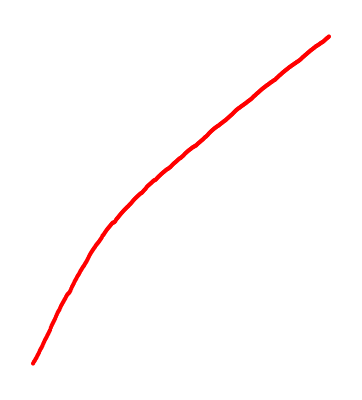

```mathematica
Show[Graphics[{
RGBColor[{1,0,0,1}],

Point[#]
}]&/@podatki]
```